1/2 (-2 ch-b (-2+y)-m (-1+x+y)^2)

1/2 (b-b y-m (-1+x+y)^2)

b-ch x-b y+ca (-1+x+y)-m (-1+x+y)^2

{0,0}

True

{1,0}

False

{0,1}

False

{0,-0.25}

False

{-1.5,0}

False

xf[{0.375,-9.98674×10^-9}]

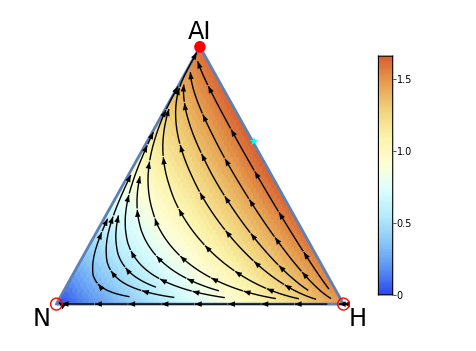

CloudObject[https://www.wolframcloud.com/obj/baumannf0/linear_m/TernaryPlot.png]

```mathematica
(* clear all variable definitions *)
Clear["Global`*"];
ClearAll["Global`*"];


(* Define the payoff matrix and vector functions *)
PayoffMatrix[x_, y_, b_, ch_, ca_, m_] := {
  {b - ch, b/2 - ch, (b + b - m (1 - x - y))/2 - ch},
  {b/2, 0, (b - m (1 - x - y))/2},
  {(b + b - m (1 - x - y))/2 - ca, (b - m (1 - x - y))/2 - ca, b - m (1 - x - y) - ca}
}
V[x_, y_] := {x, y, 1 - x - y}

(* Define Phi, Pix, and Piy *)
Phi[x_, y_, b_, ch_, ca_, m_] := V[x, y].PayoffMatrix[x, y, b, ch, ca, m].V[x, y]
Pix[x_, y_, b_, ch_, ca_, m_] := PayoffMatrix[x, y, b, ch, ca, m][[1]].V[x, y]
Piy[x_, y_, b_, ch_, ca_, m_] := PayoffMatrix[x, y, b, ch, ca, m][[2]].V[x, y]


Pix[x, y, b, ch, ca, m]//FullSimplify
Piy[x, y, b, ch, ca, m]//FullSimplify
Phi[x, y, b, ch, ca, m]//FullSimplify

(* Define the system of differential equations *)
xdot[x_, y_, b_, ch_, ca_, m_] := x (Pix[x, y, b, ch, ca, m] - Phi[x, y, b, ch, ca, m])
ydot[x_, y_, b_, ch_, ca_, m_] := y (Piy[x, y, b, ch, ca, m] - Phi[x, y, b, ch, ca, m])

(* Solve for fixed points by setting xdot and ydot to zero *) 
fixedPoints[b_, ch_, ca_, m_] := Solve[ {xdot[x, y, b, ch, ca, m] == 0, ydot[x, y, b, ch, ca, m] == 0}, {x, y} ]

(* Define the Jacobian matrix symbolically without substitution *)
JacobianReplicator[x_, y_, b_, ch_, ca_, m_] := 
 Evaluate[D[{xdot[x, y, b, ch, ca, m], ydot[x, y, b, ch, ca, m]}, {{x, y}}]]

(* Get the eigenvalues of the Jacobian and substitute values afterwards *)
EigenvaluesJacobianAtPoint[x0_, y0_, b_, ch_, ca_, m_] := Module[{jacobian, eigenvalues},
  jacobian = JacobianReplicator[x, y, b, ch, ca, m]; (* Define Jacobian symbolically *)
  eigenvalues = Eigenvalues[jacobian /. {x -> x0, y -> y0}]; (* Substitute values after *)
  eigenvalues
]

(*plot the ternary diagram for these parameters*)
ch = 2;
ca =1.5;
b=3.5;
m=0.4;

max1[ch_,ca_,m_]:= ((-ch+ca)/(2m))+1;
max1[ch,ca,m];

max2[b_,ca_,m_]:= ((-b+ca)/(2m))+1;
max2[b,ca,m];


(*...the coordinates of the *)
coordinatesEigenvalue1 = {0,0};
coordinatesEigenvalue2 = {1,0};
coordinatesEigenvalue3 = {0,1};
coordinatesEigenvalue4 = {0, (-b+2 ca+m)/m};
coordinatesEigenvalue5 = {(2 ca-2 ch+m)/m, 0};

(*eigenvalues and their stability for the parameters defined above*)
coordinatesEigenvalue1
Reduce[EigenvaluesJacobianAtPoint[coordinatesEigenvalue1[[1]], coordinatesEigenvalue1[[2]], b, ch, ca, m]<0]
coordinatesEigenvalue2
Reduce[EigenvaluesJacobianAtPoint[coordinatesEigenvalue2[[1]], coordinatesEigenvalue2[[2]], b, ch, ca, m]<0]
coordinatesEigenvalue3
Reduce[EigenvaluesJacobianAtPoint[coordinatesEigenvalue3[[1]], coordinatesEigenvalue3[[2]], b, ch, ca, m]<0]
coordinatesEigenvalue4
Reduce[EigenvaluesJacobianAtPoint[coordinatesEigenvalue4[[1]], coordinatesEigenvalue4[[2]], b, ch, ca, m]<0]
coordinatesEigenvalue5
Reduce[EigenvaluesJacobianAtPoint[coordinatesEigenvalue5[[1]], coordinatesEigenvalue5[[2]], b, ch, ca, m]<0]


(* Define the system of differential equations *)
xdotm[x_, y_] := 1/2 x (2 ch (-1+x)+b y-2 ca (-1+x+y)+m (-1+x+y)^2);
ydotm[x_, y_] := 1/2 y (2 ch x+b (-1+y)-2 ca (-1+x+y)+m (-1+x+y)^2);

(* Define coordinate transformation to fit the triangle *)
TernCoords[x_, y_] = {{1/2, -1/2}, {-Tan[Pi/3]/2, -Tan[Pi/3]/2}} . {x, y} + {1/2, Tan[Pi/3]/2};
diskradius = .03;
textoffset = .05;
thickness = .005;
ls = {FontSize -> 24, FontFamily -> "Helvetica"};
vlabels = {Graphics[
    Text[Style["N", ls], {-textoffset, -textoffset}]], 
   Graphics[Text[Style["H", ls], {1 + textoffset, -textoffset}]], 
   Graphics[
    Text[Style["AI", ls], {1/2, Tan[Pi/3]/2 + textoffset}]]};


(* Define the payoff matrix and substituted vector as functions of (x, y) *)
payoffMatrix[x_, y_] := {{b - ch, b/2 - ch, (b + b - (1 - x - y)*m)/2 - ch}, 
                         {b/2, 0, (b - (1 - x - y)*m)/2}, 
                         {(b + b - (1 - x - y)*m)/2 - ca, (b - (1 - x - y)*m)/2 - ca, b - (1 - x - y)*m - ca}};
                         
substitutedVector[x_, y_] := {x, y, 1 - x - y};

(* Define the payoff function *)
payoff[x_, y_] := substitutedVector[x, y].payoffMatrix[x, y].substitutedVector[x, y]


(* Maximize the payoff function with respect to (x, y) within valid ranges *) 
maximumValue = Maximize[{payoff[x, y], 0 ≤ x ≤1 && 0 ≤ y ≤ 1 && x + y ≤ 1}, {x, y}];

maxCoords={x,y}/. Last@maximumValue;
maxCoordsTransformed=xf[maxCoords];
maxPointGraphic=Graphics[{Cyan,Style[Text["★",maxCoordsTransformed,{0,-1}],FontSize->24]}];

maxCoordsTransformed

(* Calculate minimum and maximum payoff values across the triangular region *)
payoffRange = 
  MinMax[Flatten[Table[payoff[x, y], {x, 0, 1, 0.05}, {y, 0, 1 - x, 0.05}]]];
{minPayoff, maxPayoff} = payoffRange;
(*Maximum payoff (value + location)*)


(* Generate the stream plot in the original coordinates *)
dp = StreamPlot[
   {xdotm[x, y], ydotm[x, y]},
   {x, 0, 1}, {y, 0, 1},
   RegionFunction -> (#1 ≤ 1 - #2 &), 
   RegionFillingStyle -> None, 
   PerformanceGoal -> "Speed", 
   StreamScale -> {Large, Automatic, 0.03},
   StreamStyle -> Black, 
   StreamColorFunction -> None,
   FrameStyle -> Thick
];


(* Find the geometric transformation to align the stream plot within the triangle *)
{error, xf} = FindGeometricTransform[
   {{1, Tan[Pi/3]}/2, {0, 0}, {1, 0}}, (* Triangle vertices in target coordinates *)
   {{0, 0}, {0, 1}, {1, 0}} (* Triangle vertices in stream plot coordinates *)
];


(* Apply the transformation to the stream plot *)
ternPlot = Graphics[GeometricTransformation[First@dp, xf]];

(* Define coordinates where circles should be placed *) 
circleCoords = {{0, 0}, {1, 0},{0, 1}};
(* Function to generate filled or unfilled circles based on a Boolean list *)
fillCircles[fillList_List] := 
  Table[
    If[fillList[[i]], 
      {Red, Disk[TernCoords[circleCoords[[i, 1]], circleCoords[[i, 2]]], 0.02]}, 
      {Red, Circle[TernCoords[circleCoords[[i, 1]], circleCoords[[i, 2]]], 0.02]}
    ], 
    {i, Length[fillList]}
  ];
(* Generate circle graphics with filling according to a Boolean list *)
fillListStablePoints = {True, False,False};
circleGraphics = Graphics[fillCircles[fillListStablePoints]];  

(* Generate the color-coded payoff region plot with a color legend *)
payoffPlot = RegionPlot[
   0 ≤ x ≤ 1 && 0 ≤ y ≤ 1 - x, (* Triangle region constraint *)
   {x, 0, 1}, {y, 0, 1},
   ColorFunction -> (ColorData["LightTemperatureMap"][Rescale[payoff[#1, #2], {minPayoff, maxPayoff}]] &), 
   ColorFunctionScaling -> False,  (* Scaling is manually handled *)
   PlotPoints -> 50,
   PlotRangePadding -> None,
   BoundaryStyle -> None
];

(* Update the legend with the computed payoff range *)
legend = BarLegend[
   {"LightTemperatureMap", {minPayoff, maxPayoff}},
   LabelStyle -> Directive[FontSize -> 14]
];

(* Apply the transformation to the payoff plot to align it with the triangle *)
payoffTernPlot = Graphics[GeometricTransformation[First@payoffPlot, xf]];

(* Display the plot with the colored payoff background and legend *)
ternaryPlot=Show[Legended[Show[payoffTernPlot, ternPlot, circleGraphics, vlabels,maxPointGraphic], legend]]
CloudExport[ternaryPlot,"PNG","/linear_m/TernaryPlot.png",ImageResolution->800]
```